```mathematica
(" Here, the extinction/scattering/absorption spectra of a core-shell nanocylinder is calculated based on 
   the equations, as shown in Light scattering at oblique incidence on two coaxial cylinders,Applied Optics Vol. 33, Issue 18, pp. 4013-4024 (1994)")

xiLimit=500;
BesselJp[m_,x_]:=If[Abs[x]< xiLimit,D[BesselJ[m,x1],x1]/.{x1->x},-Sqrt[2/(Pi*x)] Sin[(x-m/2*Pi-Pi/4)]];
BesselYp[m_,x_]:=If[Abs[x]< xiLimit,D[BesselY[m,x1],x1]/.{x1->x},Sqrt[2/(Pi*x)] Cos[(x-m/2*Pi-Pi/4)]];
HankelH1p[m_,x_]:=If[Abs[x]< xiLimit,D[HankelH1[m,x1],x1]/.{x1->x},I*Sqrt[2/(Pi*x)] Exp[I*(x-m/2*Pi-Pi/4)]];
HankelH2p[m_,x_]:=If[Abs[x]< xiLimit,D[HankelH2[m,x1],x1]/.{x1->x},-I*Sqrt[2/(Pi*x)] Exp[-I*(x-m/2*Pi-Pi/4)]];

AN[m_,opt_]:=Module[{sub},
k1=ω Sqrt[ϵ1 μ1]/.opt;
k2=ω Sqrt[ϵ2 μ2]/.opt;
k3=ω Sqrt[ϵ3 μ3]/.opt;
r2=r2/.opt;
r3=r3/.opt;
BJ12=BesselJ[m,k1 r2];
BJ33=BesselJ[m,k3 r3];
BJp12=BesselJp[m,k1 r2];
BJp33=BesselJp[m,k3 r3];
HA122=HankelH1[m,k2 r2];
HA123=HankelH1[m,k2 r3];
HA212=HankelH2[m,k1 r2];
HA222=HankelH2[m,k2 r2];
HA223=HankelH2[m,k2 r3];
HAp122=HankelH1p[m,k2 r2];
HAp123=HankelH1p[m,k2 r3];
HAp212=HankelH2p[m,k1 r2];
HAp222=HankelH2p[m,k2 r2];
HAp223=HankelH2p[m,k2 r3];
M={{HA212,0, -HA222,-HA122 ,0,0,0,0},
{0,-(ⅈ k1)/(μ1 ω)HAp212, 0,0,+(ⅈ k2)/(μ2 ω)HAp222,+(ⅈ k2)/(μ2 ω)HAp122,0,0},
{(+ⅈ μ1 ω)/k1 HAp212,0,-(ⅈ μ2 ω)/k2 HAp222,-(ⅈ μ2 ω)/k2 HAp122,0,0,0,0},
{0,HA212,0,0,-HA222,-HA122,0,0 },
{0,0,HA223,HA123 ,0,0,-BJ33,0},
{0,0,+(ⅈ μ2 ω)/k2 HAp223,+(ⅈ μ2 ω)/k2 HAp123,0,0, -(ⅈ μ3 ω)/k3 BJp33,0},
{0,0,0,0,HA223,HA123,0,-BJ33},
{0,0,0,0,-(ⅈ k2)/(μ1 ω)HAp223,-(ⅈ k2)/(μ1 ω)HAp123,0,+(ⅈ k3)/(ω  μ3)BJp33}
}/.opt;

SOL={{-(ⅈ)^m×BJ12,0, -HA222,-HA122 ,0,0,0,0},
{0,-(ⅈ k1)/(μ1 ω)HAp212, 0,0,+(ⅈ k2)/(μ2 ω)HAp222,+(ⅈ k2)/(μ2 ω)HAp122,0,0},
{(-ⅈ μ1 ω)/k1((ⅈ)^m)×BJp12,0,-(ⅈ μ2 ω)/k2 HAp222,-(ⅈ μ2 ω)/k2 HAp122,0,0,0,0},
{0,HA212,0,0,-HA222,-HA122,0,0 },
{0,0,HA223,HA123 ,0,0,-BJ33,0},
{0,0,+(ⅈ μ2 ω)/k2 HAp223,+(ⅈ μ2 ω)/k2 HAp123,0,0, -(ⅈ μ3 ω)/k3 BJp33,0},
{0,0,0,0,HA223,HA123,0,-BJ33},
{0,0,0,0,-(ⅈ k2)/(μ1 ω)HAp223,-(ⅈ k2)/(μ1 ω)HAp123,0,+(ⅈ k3)/(ω  μ3)BJp33}
}/.opt;
equ=Det[SOL]/Det[M];
Return[equ];
]
```

Here, the extinction/scattering/absorption spectra of a core-shell nanocylinder is calculated based on 
   the equations, as shown in Light scattering at oblique incidence on two coaxial cylinders,Applied Optics Vol. 33, Issue 18, pp. 4013-4024 (1994)

1/500000

1/5000000

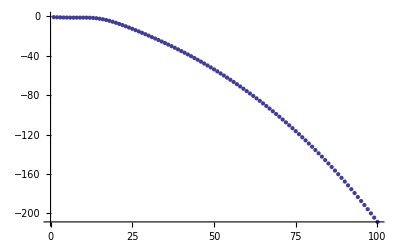

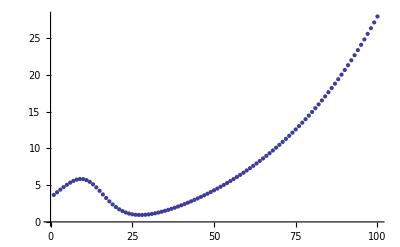

```mathematica
c = 2.99792458*10^8;(*speed of light*)
λmax=2000*10^-9  (*2000nm*)
λmin=200 *10^-9 (*200nm*)
wmax = 2*3.14159*c/(λmin);(*200nm*)
wmin = 2*3.14159*c/(λmax);(*2000nm*)
nfreq = 100;
Table[wave[i] = N[λmin+(λmax-λmin)*i/(nfreq - 1)], {i, 1,nfreq}];
Table[w[i] = 2*3.14159*c/wave[i], {i, 1, nfreq}];
epsiloninfinite=1.1156;
sigma=4.2399257866*10^16	;
A1=0.5548;
phi1=2.8463;
omega1=4.506033811*10^16;
gamma1=5.0895798919*10^16;
A2=679.7606;
phi2=-0.0998	;
omega2=3.4587148533*10^14;
gamma2=3.06427186*10^13;
A3=3.5244;
phi3=4.6586;
omega3=3.5831868337*10^15;
gamma3=1.6878397906*10^15;
Table[epsilon[i]=epsiloninfinite+sigma/(ⅈ*w[i])+A1*omega1*(Exp[ⅈ*phi1]/(omega1-w[i]-ⅈ×gamma1)+Exp[-ⅈ*phi1]/(omega1+w[i]+ⅈ×gamma1))+A2*omega2*(Exp[ⅈ*phi2]/(omega2-w[i]-ⅈ×gamma2)+Exp[-ⅈ*phi2]/(omega2+w[i]+ⅈ×gamma2))+A3*omega3*(Exp[ⅈ*phi3]/(omega3-w[i]-ⅈ×gamma3)+Exp[-ⅈ*phi3]/(omega3+w[i]+ⅈ×gamma3)),{i,1,nfreq }];
ListPlot[Table[aaa[i]=Re[epsilon[i]],{i,1,nfreq}]]
ListPlot[Table[aaa[i]=Im[epsilon[i]],{i,1,nfreq}]]
Table[nr[i]=Re[Sqrt[epsilon[i]]],{i,1,nfreq}];
Table[ni[i]=Im[Sqrt[epsilon[i]]],{i,1,nfreq}];
Table[wave[i]=10^6*(2×3.14159265×3×10^8)/w[i],{i,1,nfreq}];
Export["D:\au.dat",Table[aaa[i]=Im[epsilon[i]],{i,1,nfreq}]];
```

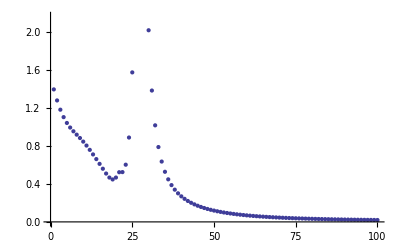

-Graphics-

```mathematica
ListPlot[EXT=Table[lambda=wave[j];
n1=1.0;
n2=nr[j]-ⅈ *ni[j] ;
n3=Sqrt[2.1] ;
opt={ω->2π/lambda,r2-> 0.05, r3-> 0.04,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(-2/(ω Sqrt[ϵ1 μ1] r2)Re[Sum[ⅈ^i×AN[i,opt]×Exp[-ⅈ×i×π],{i,-5,5}]]/.opt),{j,1,nfreq}]]
ListPlot[SCA=Table[lambda=wave[j];
n1=1.0;
n2=nr[j]-ⅈ *ni[j] ;
n3=Sqrt[2.1] ;
opt={ω->2π/lambda,r2-> 0.05, r3-> 0.04,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(-2/(ω Sqrt[ϵ1 μ1] r2)Re[Sum[ⅈ^i×AN[i,opt]×Exp[-ⅈ×i×π],{i,-5,5}]]/.opt),{j,1,nfreq}]]

Export["D:\EXT.dat",Table[EXT,{i,1,1}]];
Export["D:\SCA.dat",Table[SCA,{i,1,1}]];
Export["D:\ABS.dat",Table[EXT-SCA,{i,1,1}]];
Export["D:\wave.dat",Table[wave[i],{i,1,nfreq}]];
```

{1.65262,1.59118,1.52627,1.45741,1.38402,1.30534,1.22035,1.12763,1.02511,0.909515,0.775152,0.610296,0.383116,0.127576,0.0773229,0.0617568,0.0538879,0.0490933,0.0458769,0.043593,0.0419128,0.0406494,0.0396877,0.0389529,0.0383937,0.0379738,0.0376669,0.0374532,0.0373173,0.0372477,0.0372348,0.0372713,0.037351,0.0374689,0.0376208,0.0378033,0.0380134,0.0382486,0.0385069,0.0387862,0.0390851,0.0394021,0.039736,0.0400858,0.0404505,0.0408292,0.0412213,0.041626,0.0420427,0.042471,0.0429102,0.0433601,0.0438201,0.0442899,0.0447693,0.0452578,0.0457553,0.0462615,0.046776,0.0472989,0.0478297,0.0483684,0.0489148,0.0494687,0.05003,0.0505985,0.0511742,0.0517569,0.0523465,0.0529429,0.053546,0.0541558,0.0547721,0.0553948,0.0560239,0.0566594,0.0573011,0.0579491,0.0586032,0.0592633,0.0599295,0.0606017,0.0612799,0.0619639,0.0626538,0.0633495,0.0640511,0.0647583,0.0654713,0.06619,0.0669143,0.0676443,0.0683799,0.0691211,0.0698678,0.07062,0.0713778,0.072141,0.0729097,0.0736839,0.0744635,0.0752485,0.0760389,0.0768347,0.0776358,0.0784423,0.0792541,0.0800713,0.0808937,0.0817215,0.0825545,0.0833928,0.0842364,0.0850852,0.0859392,0.0867985,0.087663,0.0885327,0.0894076,0.0902877,0.091173,0.0920635,0.0929591,0.0938599,0.0947659,0.0956769,0.0965932,0.0975145,0.098441,0.0993726,0.100309,0.101251,0.102198,0.10315,0.104107,0.10507,0.106037,0.107009,0.107987,0.108969,0.109957,0.110949,0.111947,0.11295,0.113958,0.114971,0.115988,0.117011,0.118039,0.119072}

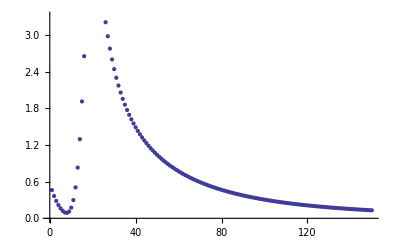

-Graphics-

```mathematica
c=2.99792458*10^8;(*光速*)
wmax=2*3.14159*c/(300*10^-9);(*300nm*)
wmin=2*3.14159*c/(1000*10^-9);(*1000nm*)
nfreq=150;
Table[wave[i]=N[300*10^-9+(i-1)*700*10^-9/(nfreq-1)],{i,1,nfreq}];
Table[w[i]=2*3.14159*c/wave[i],{i,1,nfreq}];
wp=1.5779137936666154*10^16;
epsr=9.04603;
rd=5*10^13;
Table[epsilon[i]=epsr-(wp×wp)/(w[i]×w[i]+ⅈ×rd*w[i]),{i,1,nfreq}];

Table[nr[i]=Re[Sqrt[epsilon[i]]],{i,1,nfreq}]
Table[ni[i]=Im[Sqrt[epsilon[i]]],{i,1,nfreq}];
ListPlot[EXT=Table[lambda=wave[j]*10^6;
n1=1.1;
n2=nr[j]-ⅈ ni[j] ;
n3=nr[j]-ⅈ ni[j] ;
opt={ω->2π/lambda,r2-> 0.05, r3-> 0.0001,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(-2/(ω Sqrt[ϵ1 μ1] r2)Re[Sum[ⅈ^i×AN[i,opt]×Exp[-ⅈ×i×π],{i,-5,5}]]/.opt),{j,1,150}]]
Export["D:\EXT21.dat",Table[EXT,{i,1,1}]];
ListPlot[SCA=Table[lambda=wave[j]*10^6;
n1=1.1;
n2=nr[j]-ⅈ ni[j] ;
n3=nr[j]-ⅈ ni[j] ;
opt={ω->2π/lambda,r2-> 0.05, r3-> 0.0001,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(-2/(ω Sqrt[ϵ1 μ1] r2)Re[Sum[ⅈ^i×AN[i,opt]×Exp[-ⅈ×i×π],{i,-5,5}]]/.opt),{j,1,nfreq}]]

Export["D:\SCA21.dat",Table[SCA,{i,1,1}]];
Export["D:\ABS21.dat",Table[EXT-SCA,{i,1,1}]];
Export["D:\wave.dat",Table[wave,{i,1,1}]];
```

```mathematica
Export["C:\wave.dat",Table[wave[i]=N[300*10^-9+(i-1)*700*10^-9/(nfreq-1)],{i,1,nfreq}]];
```

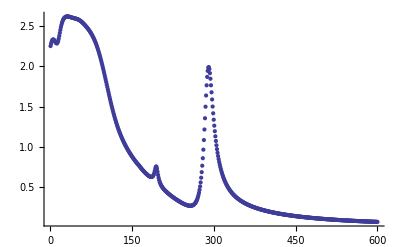

```mathematica
ListPlot[EXT=Table[lambda=wave[j];
n1=1.0;
n2=nr[j]-ⅈ ni[j] ;
n3=nr[j]-ⅈ ni[j] ;
opt={ω->2π/lambda,r2-> 0.05, r3-> 0.01,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(-2/(ω Sqrt[ϵ1 μ1] r2)Re[Sum[(ⅈ)^i×AN[i,opt]×Exp[-ⅈ×i×π],{i,-11,11}]]/.opt),{j,1,size}]]
Export["C:\EXT21.dat",Table[EXT,{i,1,1}]];
```

```mathematica
ListPlot[SCA=Table[lambda=wave[j];
n1=1.0;
n2=nr[j]-ⅈ ni[j] ;
n3=Sqrt[2.1];
opt={ω->2π/lambda,r2-> 0.135, r3-> 0.1125,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(2/(ω Sqrt[ϵ1 μ1] r2)(Abs[AN[0,opt]]^2+2*Sum[Abs[AN[i,opt]]^2,{i,1,10}])/.opt),{j,1,size}]]
ListPlot[EXT=Table[lambda=wave[j];
n1=1.0;
n2=nr[j]-ⅈ ni[j] ;
n3=Sqrt[2.1];
opt={ω->2π/lambda,r2-> 0.135, r3-> 0.1125,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(-2/(ω Sqrt[ϵ1 μ1] r2)Re[Sum[(ⅈ)^i×AN[i,opt]×Exp[-ⅈ×i×π],{i,-10,10}]]/.opt),{j,1,size}]]
Export["C:\SCA21.dat",Table[SCA,{i,1,1}]];
Export["C:\EXT21.dat",Table[EXT,{i,1,1}]];
Export["C:\ABS21.dat",Table[EXT-SCA,{i,1,1}]];
ListPlot[SCA=Table[lambda=wave[j];
n1=1.0;
n2=nr[j]-ⅈ ni[j] ;
n3=Sqrt[3.3];
opt={ω->2π/lambda,r2-> 0.135, r3-> 0.1125,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(2/(ω Sqrt[ϵ1 μ1] r2)(Abs[AN[0,opt]]^2+2*Sum[Abs[AN[i,opt]]^2,{i,1,10}])/.opt),{j,1,size}]]
ListPlot[EXT=Table[lambda=wave[j];
n1=1.0;
n2=nr[j]-ⅈ ni[j] ;
n3=Sqrt[3.3];
opt={ω->2π/lambda,r2-> 0.135, r3-> 0.1125,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(-2/(ω Sqrt[ϵ1 μ1] r2)Re[Sum[(ⅈ)^i×AN[i,opt]×Exp[-ⅈ×i×π],{i,-10,10}]]/.opt),{j,1,size}]]
Export["C:\SCA33.dat",Table[SCA,{i,1,1}]];
Export["C:\EXT33.dat",Table[EXT,{i,1,1}]];
Export["C:\ABS33.dat",Table[EXT-SCA,{i,1,1}]];
ListPlot[SCA=Table[lambda=wave[j];
n1=1.0;
n2=nr[j]-ⅈ ni[j] ;
n3=Sqrt[4.1];
opt={ω->2π/lambda,r2-> 0.135, r3-> 0.1125,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(2/(ω Sqrt[ϵ1 μ1] r2)(Abs[AN[0,opt]]^2+2*Sum[Abs[AN[i,opt]]^2,{i,1,10}])/.opt),{j,1,size}]]
ListPlot[EXT=Table[lambda=wave[j];
n1=1.0;
n2=nr[j]-ⅈ ni[j] ;
n3=Sqrt[4.1];
opt={ω->2π/lambda,r2-> 0.135, r3-> 0.1125,ϵ1->(n1^2), μ1->1.,ϵ2->n2^2, μ2->1., ϵ3->n3^2, μ3->1.};
NBG=(ω Sqrt[ϵ1 μ1]r2+10)/.opt;
T1=(-2/(ω Sqrt[ϵ1 μ1] r2)Re[Sum[(ⅈ)^i×AN[i,opt]×Exp[-ⅈ×i×π],{i,-10,10}]]/.opt),{j,1,size}]]
Export["C:\SCA41.dat",Table[SCA,{i,1,1}]];
Export["C:\EXT41.dat",Table[EXT,{i,1,1}]];
Export["C:\ABS41.dat",Table[EXT-SCA,{i,1,1}]];
```